{{10,0.411681},{100,0.176319},{1000,0.0376},{10000,0.0130015},{100000,0.003312}}

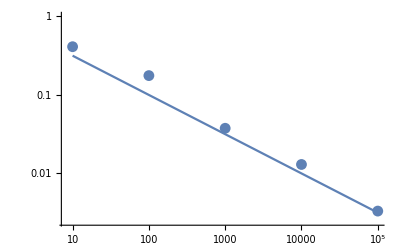

```mathematica
Clear["Global'*"];
d={};
For[t=1,t≤5,t++,
n=10^t;
f={};
For[q=1,q≤ 10,q++,
k=0.0;
For[i=0,i<n,i++,
x= RandomReal[]; 
y= RandomReal[]; 
If[x^2+ y^2≤1,k+=1.0];
]
f=Append[f,Abs[((4*k))/n-Pi]];
]
d=Append[d,{n,Mean[f]}];
]
Print[d];
dat=ListLogLogPlot[d];
diff=LogLogPlot[1/Sqrt[u],{u,10,10^5}];
Show[dat,diff]
```